# Construction of MST complete interaction bubbles

## Generate perfect 1-factorizations of the complete graph using backtracking, recursion, pruning, randomization, etc.

```mathematica
SetDirectory@NotebookDirectory[];
```

## Estimating the number of graphs

Number of colorings of the complete graph on n vertices with n-1 colors

```mathematica
Table[(n-1)^Binomial[n,2],{n,2,8,2}]
```

{1,729,30517578125,459986536544739960976801}

Choose all edges of the first color, then the second one, etc

```mathematica
Table[Product[Binomial[Binomial[n,2]-i n/2,n/2],{i,0,n-2}],{n,2,8,2}]
```

{1,90,168168000,66475579247327250000}

Choose coloring of the first node, then the next one, etc

```mathematica
Table[Product[i!,{i,n-1}],{n,2,8,2}]
```

{1,12,34560,125411328000}

## Bubble construction

### Generating all matchings

Generating all the matchings (1-factors of the complete graph with n vertices) is equivalent to generating all possible Wick contractions of n fields, hence the name of this function.

```mathematica
ClearAll@Wick;
Wick[{}]={{}};
Wick[l_]:=
Flatten[Table[
Prepend[#,{l⟦1⟧,l⟦i⟧}]&/@Wick@Drop[l⟦2;;⟧,{i-1}]
,{i,2,Length@l}],1]
```

```mathematica
ClearAll@Factors;
Factors[n_Integer]:=Factors[n]=Wick@Range@n;
```

### Building compatibility matrices

The compatibility matrix tells us if two 1-factors can be used in the same factorization. We use the asymmetric version to speed up the algorithm by choosing a specific order in which factors should be added.

```mathematica
ClearAll@CompatibilityMatrix;
CompatibilityMatrix[n_Integer]:=CompatibilityMatrix[n]=
FromDigits[#,2]&/@Table[
If[OrderedQ@{f1,f2},Boole[Intersection[f1,f2]==={}],0]
,{f1,Factors@n},{f2,Factors@n}];
```

We may want to recover the symmetric compatibility matrix for some purposes

```mathematica
ClearAll@SymmetricCompatibilityMatrix;
SymmetricCompatibilityMatrix[n_Integer]:=SymmetricCompatibilityMatrix[n]=
With[{m=IntegerDigits[#,2,(n-1)!!]&/@CompatibilityMatrix[n]},FromDigits[#,2]&/@(m+Transpose@m)]
```

We can actually cook up a compatibility matrix that incorporates the MST condition checking.

```mathematica
ClearAll@CompatibilityMatrix2;
CompatibilityMatrix2[n_Integer]:=CompatibilityMatrix2[n]=
FromDigits[#,2]&/@ParallelTable[
If[OrderedQ@{f1,f2},Boole[Intersection[f1,f2]==={}&&ConnectedGraphQ@Graph@Join[f1,f2]],0]
,{f1,Factors@n},{f2,Factors@n}];
```

#### Pre-computed matrices for n=12

```mathematica
(*Export["CompMatrix_r12.m",CompatibilityMatrix@12]*)
```

```mathematica
CompatibilityMatrix[12]=Import["CompMatrix_r12.m"];
```

```mathematica
(*Export["CompMatrix2_r12.m",CompatibilityMatrix2@12]*)
```

```mathematica
CompatibilityMatrix2[12]=Import["CompMatrix2_r12.m"];
```

### Checking MST

```mathematica
MaximallySingleTraceQ[c_Integer,m_]:=And@@Flatten@Table[ConnectedGraphQ@Graph@Join[Position[m,c],Position[m,j]],{j,c-1}]
```

### Step filtering (optional)

Using the asymmetric compatibility matrices, the 1-factors form a directed acyclic graph (DAG).
Paths in this graph are counted by entries in the matrix-power of the compatibility matrix: (C^k)_ij is the number of paths from factor i to factor j using k+1 factors in total.
The longest path in the DAG has n-1 factors, i.e. there is no path with n factors in total: C^(n-1) = 0_((n-1)!! x (n-1)!!)
We can argue that each 1-factor has a specific “time” or level in which it should be incorporated to the graph: if we add it too early, it will impose too many constraints on the next ones, if we add it too late there won’t be enough compatible 1-factors to finish.
We compute a level mask by looking at which 1-factos are never again accessible after a given number of steps.

```mathematica
ClearAll@CompatibilityMatrixPower;
CompatibilityMatrixPower[n_Integer,0]:=UnitVector[(n-1)!!,1];
CompatibilityMatrixPower[n_Integer,e_Integer]:=CompatibilityMatrixPower[n,e]=CompatibilityMatrixPower[n,e-1].(IntegerDigits[#,2,(n-1)!!]&/@CompatibilityMatrix@n)//Unitize;
```

```mathematica
ClearAll@LevelMask;
LevelMask[n_Integer,c_Integer]:=
CompatibilityMatrixPower[n,c-1]-Sum[CompatibilityMatrixPower[n,e],{e,c,n-1}]//Positive//Boole//FromDigits[#,2]&
```

```mathematica
ClearAll@CompatibilityMatrixPower2;
CompatibilityMatrixPower2[n_Integer,0]:=UnitVector[(n-1)!!,1];
CompatibilityMatrixPower2[n_Integer,e_Integer]:=CompatibilityMatrixPower2[n,e]=CompatibilityMatrixPower2[n,e-1].(IntegerDigits[#,2,(n-1)!!]&/@CompatibilityMatrix2@n)//Unitize;
```

```mathematica
ClearAll@LevelMask2;
LevelMask2[n_Integer,c_Integer]:=LevelMask2[n,c]=
CompatibilityMatrixPower2[n,c-1]-Sum[CompatibilityMatrixPower2[n,e],{e,c,n-1}]//Positive//Boole//FromDigits[#,2]&
```

### Isomorphism checking

ColorMatrix takes a list of 1-factors and builds an adjacency matrix A where A_ij is the color of the edge i<->j

```mathematica
ColorMatrix[n_Integer,p_List]:=
Block[{m=ConstantArray[0,{n,n}],c=0},
Normal@Sum[
c++;
c AdjacencyMatrix@Graph@Factors[n]⟦f⟧
,{f,p}]
]
```

FromColorMatrix reconstructs a list of 1-factors from the given color matrix (the inverse operation of ColorMatrix).

```mathematica
FromColorMatrix[n_Integer,m_]:=Sort@Flatten@Table[FirstPosition[Factors@n,Sort@DeleteDuplicates[Sort/@Position[m,c]]],{c,n-1}]
```

CanonicalColoring finds a canonical representation of the adjacency matrix to check for bubble isomorphism (using only the color permutations in plist).
This is a very slow function, nauty would do much better!

```mathematica
ClearAll@CanonicalColoring;
CanonicalColoring[n_Integer,m_][plist_List]:=
Min@Table[
Block[{newm=m⟦p,p⟧},
newm=Replace[newm,First@#->Last@#&/@Transpose@{First@newm,Range@n-1},{2}];
FromDigits[Flatten@newm,n]
]
,{p,plist}]
```

FromCanonicalColoring recovers an adjacency matrix from its canonical representation.

```mathematica
FromCanonicalColoring[n_Integer,id_Integer]:=Partition[IntegerDigits[id,n,n^2],n];
```

```mathematica
ClearAll@PartialCanonicalColoring;
PartialCanonicalColoring[n_Integer,c_Integer,m_]:=Min@Table[FromDigits[Flatten@m⟦p,p⟧,c+1],{p,Permutations@Range@n}]
```

These are subsets of permutations we may want to try.

```mathematica
ClearAll@Perms
Perms[n_Integer]:=Perms[n]=PermutationList[#,n]&/@GroupElements@GraphAutomorphismGroup@Graph@Partition[Range@n,2]
```

```mathematica
ClearAll@Perms2;
Perms2[n_Integer]:=Perms2[n]=Sort[Flatten/@Flatten[Permutations/@Factors@n,1]];
```

### Bubble generation

GenerateBubbles is the basic recursive generator

```mathematica
ClearAll@GenerateBubbles;
GenerateBubbles[n_Integer,1]:={{1}};
GenerateBubbles[n_Integer,c_Integer]:=GenerateBubbles[n,c]=
Select[
Flatten[Table[
Block[{m=CompatibilityMatrix[n]⟦b⟧,p},
p=Select[Range[(n-1)!!]IntegerDigits[BitAnd@@m,2,(n-1)!!],Positive];
Append[b,#]&/@p
]
,{b,GenerateBubbles[n,c-1]}],1]
,MaximallySingleTraceQ[c,ColorMatrix[n,#]]&]
```

GenerateBubbles2 incorporates level masks to speed up the computations

```mathematica
ClearAll@GenerateBubbles2;
GenerateBubbles2[n_Integer,1]:={{1}};
GenerateBubbles2[n_Integer,c_Integer]:=GenerateBubbles2[n,c]=
Select[
Flatten[Table[
Block[{m=CompatibilityMatrix[n]⟦b⟧,p},
p=Select[Range[(n-1)!!]IntegerDigits[BitAnd[LevelMask[n,c],BitAnd@@m],2,(n-1)!!],Positive];
Append[b,#]&/@p
]
,{b,GenerateBubbles2[n,c-1]}],1]
,MaximallySingleTraceQ[c,ColorMatrix[n,#]]&]
```

GenerateBubbles3 uses the compatibility matrix to also account for the MST condition

```mathematica
ClearAll@GenerateBubbles3;
GenerateBubbles3[n_Integer,1]:={{1}};
GenerateBubbles3[n_Integer,c_Integer]:=GenerateBubbles3[n,c]=
Flatten[Table[
Block[{m=CompatibilityMatrix2[n]⟦b⟧,p},
p=Select[Range[(n-1)!!]IntegerDigits[BitAnd[LevelMask[n,c],BitAnd@@m],2,(n-1)!!],Positive];
Append[b,#]&/@p
]
,{b,GenerateBubbles3[n,c-1]}],1]
```

### Results

#### n=6

There is a unique n=6 complete MST interaction bubble, up to isomorphisms.

```mathematica
Length/@Table[GenerateBubbles[6,c],{c,5}]//AbsoluteTiming
```

{0.0103307,{1,8,16,8,2}}

```mathematica
Length/@Table[GenerateBubbles2[6,c],{c,5}]//AbsoluteTiming
```

{0.0037722,{1,2,2,2,2}}

```mathematica
Length/@Table[GenerateBubbles3[6,c],{c,5}]//AbsoluteTiming
```

{0.0002578,{1,2,2,2,2}}

```mathematica
DeleteDuplicatesBy[GenerateBubbles2[6,5],CanonicalColoring[6,ColorMatrix[6,#]][Perms@6]&]
```

{{1,5,9,11,13}}

```mathematica
Length@%
```

1

#### n=8

There is a unique n=8 complete MST interaction bubble, up to isomorphisms.

```mathematica
Length/@Table[GenerateBubbles[8,c],{c,7}]//AbsoluteTiming
```

{2.25091,{1,48,480,1280,1152,384,64}}

```mathematica
Length/@Table[GenerateBubbles2[8,c],{c,7}]//AbsoluteTiming
```

{0.266846,{1,8,32,64,72,64,64}}

```mathematica
Length/@Table[GenerateBubbles3[8,c],{c,7}]//AbsoluteTiming
```

{0.0884537,{1,8,32,64,72,64,64}}

```mathematica
DeleteDuplicatesBy[GenerateBubbles2[8,7],CanonicalColoring[8,ColorMatrix[8,#]][Perms@8]&]
```

{{1,20,39,56,75,77,94}}

```mathematica
Length@%
```

1

#### n=10

There is a unique n=10 complete MST interaction bubble, up to isomorphisms.

```mathematica
Length/@Table[GenerateBubbles3[10,c],{c,9}]//AbsoluteTiming
```

{35.9258,{1,48,960,8640,28432,39712,18112,864,864}}

```mathematica
DeleteDuplicatesBy[GenerateBubbles2[10,9],CanonicalColoring[10,ColorMatrix[10,#]][Perms@10]&]
```

{{1,125,249,341,433,605,731,823,909},{1,125,254,366,522,605,657,737,926}}

```mathematica
Length@%
```

2

```mathematica
DeleteDuplicatesBy[%%,CanonicalColoring[10,ColorMatrix[10,#]][Perms2@10]&]
```

{{1,125,249,341,433,605,731,823,909}}

```mathematica
Length@%
```

1

#### n=12

With the right isomorphism checking function, we should find there are 5 inequivalent n=12 bubbles

```mathematica
First@GenerateBubbles2[12,2]
```

{1,1070}

```mathematica
GenerateBubbles3[12,2]={{1,1070}};
```

```mathematica
Length@GenerateBubbles3[12,3]
```

148

```mathematica
Length@GenerateBubbles3[12,4]
```

8080

```mathematica
Length@GenerateBubbles3[12,5]
```

167072

```mathematica
Length@GenerateBubbles3[12,6]
```

1127348

```mathematica
Length@GenerateBubbles3[12,7]
```

2026215

```mathematica
Length@GenerateBubbles3[12,8]
```

944190

```mathematica
Length@GenerateBubbles3[12,9]
```

91388

```mathematica
Length@GenerateBubbles3[12,10]
```

2840

```mathematica
Length@GenerateBubbles3[12,11]
```

1752

```mathematica
Export["Bubbles_n12.m",GenerateBubbles3[12,11]]
```

Bubbles_n12.m

```mathematica
DeleteDuplicatesBy[GenerateBubbles3[12,11],CanonicalColoring[12,ColorMatrix[12,#]][Perms@12]&]
```

{{1,1070,2139,3210,4592,5670,5729,6756,8110,9334,10119},{1,1070,2139,3312,4698,5435,6459,7136,7615,9178,9559},{1,1070,2139,3327,4404,5434,6566,7063,8335,8683,9462},{1,1070,2139,3402,4509,5670,6479,7206,8003,8630,9451},{1,1070,2139,3444,4455,5655,6506,7058,8151,8507,9574},{1,1070,2141,2991,3866,5398,6287,7541,8346,8949,10080},{1,1070,2141,3201,4283,5555,6224,7511,7563,8699,10228},{1,1070,2141,3210,4647,5322,6498,6805,7611,9281,10024},{1,1070,2141,3314,4651,4749,6296,7437,7751,8949,10229},{1,1070,2141,3445,4274,5587,6498,6668,7701,8991,10228},{1,1070,2141,3659,4179,5348,6559,7164,7563,8678,10228},{1,1070,2141,3669,4390,5587,6341,6630,8054,8698,10025},{1,1070,2141,3699,4507,5490,5833,7196,7571,9215,9975},{1,1070,2144,3357,4496,5278,5844,7397,8443,8560,9936},{1,1070,2156,3034,4175,5541,5736,7517,8126,9163,10241},{1,1070,2156,3215,4575,4927,6324,6698,8491,9186,10015},{1,1070,2233,3430,4721,4795,6394,7169,8358,8888,9594},{1,1070,2258,3418,4239,5457,6483,6803,8443,8840,9474}}

```mathematica
Length@%
```

18

```mathematica
DeleteDuplicatesBy[%%,CanonicalColoring[12,ColorMatrix[12,#]][Perms2@12]&]
```

{{1,1070,2139,3210,4592,5670,5729,6756,8110,9334,10119},{1,1070,2139,3312,4698,5435,6459,7136,7615,9178,9559},{1,1070,2139,3327,4404,5434,6566,7063,8335,8683,9462},{1,1070,2139,3402,4509,5670,6479,7206,8003,8630,9451},{1,1070,2139,3444,4455,5655,6506,7058,8151,8507,9574},{1,1070,2141,2991,3866,5398,6287,7541,8346,8949,10080},{1,1070,2141,3201,4283,5555,6224,7511,7563,8699,10228},{1,1070,2141,3210,4647,5322,6498,6805,7611,9281,10024},{1,1070,2141,3314,4651,4749,6296,7437,7751,8949,10229},{1,1070,2141,3445,4274,5587,6498,6668,7701,8991,10228},{1,1070,2141,3659,4179,5348,6559,7164,7563,8678,10228},{1,1070,2141,3669,4390,5587,6341,6630,8054,8698,10025},{1,1070,2141,3699,4507,5490,5833,7196,7571,9215,9975},{1,1070,2144,3357,4496,5278,5844,7397,8443,8560,9936},{1,1070,2156,3034,4175,5541,5736,7517,8126,9163,10241},{1,1070,2156,3215,4575,4927,6324,6698,8491,9186,10015},{1,1070,2233,3430,4721,4795,6394,7169,8358,8888,9594},{1,1070,2258,3418,4239,5457,6483,6803,8443,8840,9474}}

```mathematica
Length@%
```

18

## Random bubble construction

Random generation of bubbles (we use the symmetric compatibility matrix to avoid skewing our choices)

```mathematica
ClearAll@GenerateRandomBubble;
GenerateRandomBubble[n_Integer,1]:={1};
GenerateRandomBubble[n_Integer,c_Integer]:=
Block[{b=GenerateRandomBubble[n,c-1],m,p,res},
m=SymmetricCompatibilityMatrix[n]⟦b⟧;
p=Select[Range[(n-1)!!]IntegerDigits[BitAnd@@m,2,(n-1)!!],Positive];
If[p=={},
GenerateRandomBubble[n,c],
res=Append[b,RandomChoice@p];
If[!MaximallySingleTraceQ[c,ColorMatrix[n,res]],
GenerateRandomBubble[n,c],
res
]
]
]
```

Random generation of bubbles using level masks, but otherwise same as above

```mathematica
ClearAll@GenerateRandomBubble2;
GenerateRandomBubble2[n_Integer,1]:={1};
GenerateRandomBubble2[n_Integer,c_Integer]:=
Block[{b=GenerateRandomBubble2[n,c-1],m,p,res},
If[c≥9,Print@c];
m=SymmetricCompatibilityMatrix[n]⟦b⟧;
p=Select[Range[(n-1)!!]IntegerDigits[BitAnd[LevelMask[n,c],BitAnd@@m],2,(n-1)!!],Positive];
If[p=={},
GenerateRandomBubble2[n,c],
res=Append[b,RandomChoice@p];
If[!MaximallySingleTraceQ[c,ColorMatrix[n,res]],
GenerateRandomBubble2[n,c],
res
]
]
]
```

Random generation of bubbles using level masks, but otherwise same as above

```mathematica
Do[
TotTime[c]=0;
NumGen[c]=0;
,{c,11}]
```

```mathematica
ClearAll@GenerateRandomBubbleTiming;
GenerateRandomBubbleTiming[n_Integer,1]:={1};
GenerateRandomBubbleTiming[n_Integer,c_Integer]:=
Block[{b,m,p,res,time},
{time,b}=AbsoluteTiming@GenerateRandomBubbleTiming[n,c-1];
TotTime[c-1]+=time;
NumGen[c-1]++;
m=SymmetricCompatibilityMatrix[n]⟦b⟧;
p=Select[Range[(n-1)!!]IntegerDigits[BitAnd[LevelMask[n,c],BitAnd@@m],2,(n-1)!!],Positive];
If[p=={},
GenerateRandomBubbleTiming[n,c],
res=Append[b,RandomChoice@p];
If[!MaximallySingleTraceQ[c,ColorMatrix[n,res]],
GenerateRandomBubbleTiming[n,c],
res
]
]
]
```

```mathematica
GenerateRandomBubble2[10,9]//AbsoluteTiming
```

{14.4896,{1,182,311,371,449,531,684,769,921}}

```mathematica
GenerateRandomBubbleTiming[10,9]//AbsoluteTiming
```

{20.3488,{1,196,260,399,491,569,648,740,897}}

```mathematica
GenerateRandomBubbleTiming[12,5]//AbsoluteTiming
```

{1.24415,{1,1435,2194,3519,4142}}

```mathematica
GenerateRandomBubbleTiming[12,6]//AbsoluteTiming
```

{0.417018,{1,1070,2575,3694,4167,4778}}

```mathematica
GenerateRandomBubbleTiming[12,7]//AbsoluteTiming
```

{33.5892,{1,1753,2194,2937,4675,4915,5920}}

```mathematica
GenerateRandomBubbleTiming[12,8]//AbsoluteTiming
```

{517.003,{1,1615,2299,3643,4697,4815,5964,6770}}

```mathematica
GenerateRandomBubbleTiming[12,9]//AbsoluteTiming
```

$Aborted

```mathematica
GenerateRandomBubbleTiming[12,10]//AbsoluteTiming
```

```mathematica
GenerateRandomBubbleTiming[12,11]//AbsoluteTiming
```

```mathematica
Table[TotTime@c,{c,8}]
```

{0.416002,2312.22,3831.71,4463.53,4627.69,4640.87,4251.34,1657.97}

```mathematica
Table[NumGen@c,{c,8}]
```

{516137,327938,133058,34247,5678,616,55,1}

```mathematica
%%/%
```

{8.05991×10^-7,0.00705077,0.0287973,0.130334,0.81502,7.53388,77.2971,1657.97}

## Plots for the problem statement

```mathematica
ClearAll@Colors;
Colors[3][i_]:={Red,Green,Blue}⟦i⟧;
Colors[5][i_]:={Red,Green,Blue,Black,Cyan}⟦i⟧;
```

```mathematica
Coloring[m_]:=
With[{n=Length@m},
CompleteGraph[n,EdgeStyle->Flatten@Table[i<->j->Colors[n-1][m⟦i,j⟧],{i,n},{j,i-1}]]
]
```

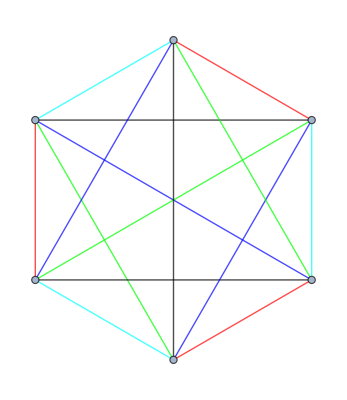

```mathematica
Coloring@ColorMatrix[6,First@GenerateBubbles[6,5]]
```

```mathematica
Export["cMSTr5.pdf",%]
```

cMSTr5.pdf

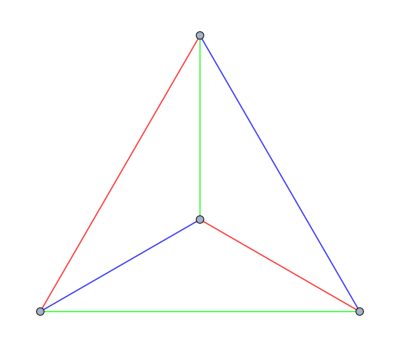

```mathematica
Coloring@ColorMatrix[4,First@GenerateBubbles[4,3]]
```

```mathematica
Export["tetrahedral.pdf",%]
```

tetrahedral.pdf

```mathematica
Graph[{1<->2,1<->2,1<->2}]
```

-Graphics-

```mathematica
Export["simple.pdf",%]
```

simple.pdf

```mathematica
Graph[{1<->2,1<->2,1<->3,2<->4,3<->4,3<->4}]
```

-Graphics-

```mathematica
Export["pillow.pdf",%]
```

pillow.pdf